-Graphics3D-

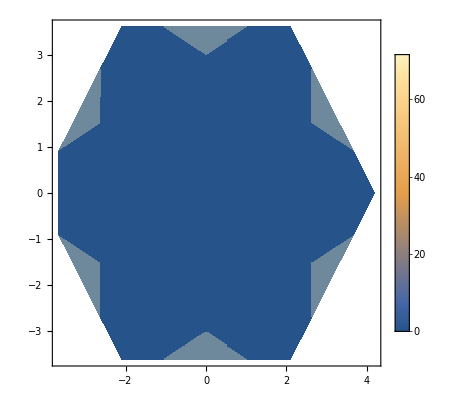

```mathematica
(*data import*)
dataLoc=StringJoin[NotebookDirectory[],"dataOut/strFct.dat"];
dataStrFct=Import[dataLoc];
(*basic settings*)
numCellX=12;
numCellY=12;
(*******************************************************************)
numCell=numCellX numCellY;
sphToCar[coorSph_]:={Sin[coorSph⟦1⟧]Cos[coorSph⟦2⟧],Sin[coorSph⟦1⟧]Sin[coorSph⟦2⟧],Cos[coorSph⟦1⟧]};
coorToCode[coor_]:=1+coor⟦1⟧+coor⟦2⟧numCellX+coor⟦3⟧numCell;
codeToCoor[code_]:=Module[{remain,coor1,coor2,coor3},
remain=code-1;
coor3=Floor[remain/numCell];
remain=remain-coor3 numCell;
coor2=Floor[remain/numCellX];
coor1=remain-coor2 numCellX;
{coor1,coor2,coor3}
];
err[data_]:=Module[{len,sumSq,meanData},
len=Length[data];
sumSq=Sum[data⟦i⟧^2,{i,1,len}];
meanData=Mean[data];
√((sumSq-len meanData^2)/(len(len-1)))
];
uniX={1,0}//N;
uniY={1/2,(√3)/2}//N;
uniC={0,1/(√3)}//N;
uniKX=(4 √3 π)/(3numCellX){(√3)/2,-1/2}//N;
uniKY=(4 √3 π)/(3numCellY){0,1}//N;
vecRListA=Table[Module[{coorTemp},
coorTemp=codeToCoor[i];
coorTemp⟦1⟧uniX+coorTemp⟦2⟧uniY
],{i,1,numCell}];
vecRListB=Table[Module[{coorTemp},
coorTemp=codeToCoor[i+numCell];
coorTemp⟦1⟧uniX+coorTemp⟦2⟧uniY+uniC
],{i,1,numCell}];
vecRList=Join[vecRListA,vecRListB];
vecKList=Table[Module[{coorTemp},
coorTemp=codeToCoor[i];
coorTemp⟦1⟧uniKX+coorTemp⟦2⟧uniKY
],{i,1,numCell}];
uniKX=(4 √3 π)/(3numCellX){(√3)/2,-1/2}//N;
uniKY=(4 √3 π)/(3numCellY){0,1}//N;
vecKList=Table[Module[{coorTemp},
coorTemp=codeToCoor[i];
coorTemp⟦1⟧uniKX+coorTemp⟦2⟧uniKY
],{i,1,numCell}];
(*define the first Brillouin zone*)
cornorList={
2π{1/3,(√3)/3},
-2π{1/3,(√3)/3},
2π{-1/3,(√3)/3},
-2π{-1/3,(√3)/3},
2π{2/3,0},
-2π{2/3,0}
}//N;
borderList={
{cornorList⟦1⟧,cornorList⟦5⟧},
{cornorList⟦5⟧,cornorList⟦4⟧},
{cornorList⟦4⟧,cornorList⟦2⟧},
{cornorList⟦2⟧,cornorList⟦6⟧},
{cornorList⟦6⟧,cornorList⟦3⟧},
{cornorList⟦3⟧,cornorList⟦1⟧}
};
graBZ=Graphics[{Red,Line[borderList]}];
strFacGen[dataStr_]:=Module[{data1,data2,data3,data4},
data1=Table[Append[vecKList⟦i⟧,dataStr⟦i,3⟧],{i,1,numCell}];
data2=Table[Append[vecKList⟦i⟧-uniKX numCellX,dataStr⟦i,3⟧],{i,1,numCell}];
data3=Table[Append[vecKList⟦i⟧-uniKY numCellY,dataStr⟦i,3⟧],{i,1,numCell}];
data4=Table[Append[vecKList⟦i⟧-uniKX numCellX-uniKY numCellY,dataStr⟦i,3⟧],{i,1,numCell}];
Join[data1,data2,data3,data4]
];
strFac=strFacGen[dataStrFct];
pointIn={};
Table[Module[{data,judA,judB,jud},
data=strFac⟦pointInd⟧;
judA=Product[If[data⟦2⟧≤(borderList⟦i,2,2⟧-borderList⟦i,1,2⟧)/(borderList⟦i,2,1⟧-borderList⟦i,1,1⟧)(data⟦1⟧-borderList⟦i,1,1⟧)+borderList⟦i,1,2⟧,1,0],{i,{1,5,6}}];
judB=Product[If[data⟦2⟧≥(borderList⟦i,2,2⟧-borderList⟦i,1,2⟧)/(borderList⟦i,2,1⟧-borderList⟦i,1,1⟧)(data⟦1⟧-borderList⟦i,1,1⟧)+borderList⟦i,1,2⟧,1,0],{i,{2,3,4}}];
jud=judA judB;
If[jud==1,pointIn=Append[pointIn,pointInd]];
],{pointInd,1,Length[strFac]}];
strFacIn=Table[strFac⟦i⟧,{i,pointIn}];
gra3D=ListPlot3D[strFacIn,PlotRange->All,Mesh->None,ColorFunction->"TemperatureMap",Boxed->False,Axes->{True,True,False},AxesLabel->{"k_x","k_y"}];
graDen=ListDensityPlot[strFacIn,PlotRange->All,PlotLegends->Automatic];
Export[StringJoin[NotebookDirectory[],"strFct3D.eps"],gra3D];
Export[StringJoin[NotebookDirectory[],"strFctDen.eps"],graDen];
Export[StringJoin[NotebookDirectory[],"strFct3D.png"],gra3D];
Export[StringJoin[NotebookDirectory[],"strFctDen.png"],graDen];
Show[gra3D]
Show[graDen]
```

```mathematica
1192/288//N
```

4.13889

```mathematica
ArcCos[(√3)/3]
```

ArcCos[1/(√3)]

```mathematica
matR1={
{Cos[π/4],Sin[π/4],0},
{-Sin[π/4],Cos[π/4],0},
{0,0,1}
};
matR2={
{(√3)/3,0,-(√6)/3},
{0,1,0},
{(√6)/3,0,(√3)/3}
};
matR=matR2.matR1;
```

```mathematica
matR//MatrixForm
```

(1/(√6) | 1/(√6) | -√(2/3)
-1/(√2) | 1/(√2) | 0
1/(√3) | 1/(√3) | 1/(√3))

```mathematica
matItacA={
{-2.167,0,1.886},
{0,-1.5,0},
{1.886,0,-0.833}
};
```

```mathematica
Inverse[matR].matItacA.matR//MatrixForm
```

(-0.499764 | 1.00024 | 0.000132204
1.00024 | -0.499764 | 0.000132204
0.000132204 | 0.000132204 | -3.50047)

```mathematica
matItacB={
{-1.667,0.289,-0.943},
{0.289,-2,1.633},
{-0.943,1.633,-0.833}
};
```

```mathematica
Inverse[matR].matItacB.matR//MatrixForm
```

(-3.50023 | -0.0000344631 | 0.000452001
-0.0000344631 | -0.499841 | 1.00008
0.000452001 | 1.00008 | -0.499931)

```mathematica
vecT1={
{0},
{0},
{1}
};
vecT2={
{0.903},
{0},
{-0.431}
};
vecT3={
{-0.452},
{0.782},
{-0.431}
};
vecT4={
{0},
{0},
{-1}
};
vecT5={
{-0.451},
{-0.782},
{-0.431}
};
vecT6={
{-0.903},
{0},
{0.431}
};
vecT7={
{0.451},
{-0.782},
{0.431}
};
vecT8={
{0.451},
{0.782},
{0.431}
};
```

```mathematica
Inverse[matR].vecT1//MatrixForm
```

(1/(√3)
1/(√3)
1/(√3))

```mathematica
Inverse[matR].vecT2//MatrixForm
```

(0.11981
0.11981
-0.986134)

```mathematica
Inverse[matR].vecT3//MatrixForm
```

(-0.986324
0.119591
0.120218)

```mathematica
Inverse[matR].vecT4//MatrixForm
```

(-1/(√3)
-1/(√3)
-1/(√3))

```mathematica
Inverse[matR].vecT5//MatrixForm
```

(0.12
-0.985915
0.119402)

```mathematica
Inverse[matR].vecT6//MatrixForm
```

(-0.11981
-0.11981
0.986134)

```mathematica
Inverse[matR].vecT7//MatrixForm
```

(0.985915
-0.12
-0.119402)

```mathematica
Inverse[matR].vecT8//MatrixForm
```

(-0.12
0.985915
-0.119402)

```mathematica
vecT={vecT1,vecT2,vecT3,vecT4,vecT5,vecT6,vecT7,vecT8};
vecS=Table[Inverse[matR].vecT⟦i⟧,{i,1,Length[vecT]}];
```

```mathematica
vecPlnT=Table[{vecT⟦i,1,1⟧,vecT⟦i,2,1⟧,vecT⟦i,3,1⟧},{i,1,Length[vecT]}];
vecPlnS=Table[Inverse[matR].vecPlnT⟦i⟧,{i,1,Length[vecPlnT]}];
```

```mathematica
vecPlnS
```

{{1/(√3),1/(√3),1/(√3)},{0.11981,0.11981,-0.986134},{-0.986324,0.119591,0.120218},{-1/(√3),-1/(√3),-1/(√3)},{0.12,-0.985915,0.119402},{-0.11981,-0.11981,0.986134},{0.985915,-0.12,-0.119402},{-0.12,0.985915,-0.119402}}

```mathematica
carToSph[spinCar_]:=Module[{pol,azi},
pol=ArcCos[spinCar⟦3⟧];
azi=0;
If[spinCar⟦2⟧>0,{
azi=ArcCos[spinCar⟦1⟧/(√(1-spinCar⟦3⟧^2))];
},{
azi=2π-ArcCos[spinCar⟦1⟧/(√(1-spinCar⟦3⟧^2))];
}];
{pol,azi}
];
```

```mathematica
spinSphList=Table[carToSph[vecPlnS⟦i⟧]//N,{i,1,Length[vecPlnS]}];
```

```mathematica
spinSphList//MatrixForm
```

(0.955317 | 0.785398
2.97487 | 0.764149
1.45029 | 3.02777
2.18628 | 3.92699
1.45111 | 4.83355
0.16672 | 3.90574
1.69048 | 6.16496
1.69048 | 1.69196)

```mathematica
vecPlnS//N//MatrixForm
```

(0.57735 | 0.57735 | 0.57735
0.11981 | 0.11981 | -0.986134
-0.986324 | 0.119591 | 0.120218
-0.57735 | -0.57735 | -0.57735
0.12 | -0.985915 | 0.119402
-0.11981 | -0.11981 | 0.986134
0.985915 | -0.12 | -0.119402
-0.12 | 0.985915 | -0.119402)

```mathematica
Transpose[vecT2].matItacA.vecT4
```

{{-2.06208}}

```mathematica
Transpose[vecS⟦2⟧].Inverse[matR].matItacA.matR.vecS⟦4⟧
```

{{-2.06208}}

```mathematica
Transpose[vecS⟦3⟧].Inverse[matR].matItacB.matR.vecS⟦4⟧
```

{{-2.06227}}